```mathematica
HalfDiv[func_,R_]:= Module[{res},
a=-5;
b=5;
e=0.001;
While[b-a>e,
res=func[(b+a)/2];
If[res>R, b= (b+a)/2,a=(b+a)/2];
];
yr=N[(b+a)/2]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
fun=Import["C:\\Users\\Yawor\\OneDrive\\Рабочий стол\\fun.wdx","wdx"];
count=50;
data=Array[0&,{count,3}];
fx[x_]:=Integrate[fun[xsh,y],{xsh,-5,x},{y,-5,5}];
Do[
R1=Random[];
xr=HalfDiv[fx,R1];
fy[y_]:=Integrate[fun[xr,ysh],{ysh,-5,y}];
mu=fy[5];
R2=Random[] mu;
yr=HalfDiv[fy,R2];
data[[i]]={xr,yr};
,{i,1,count}]
```

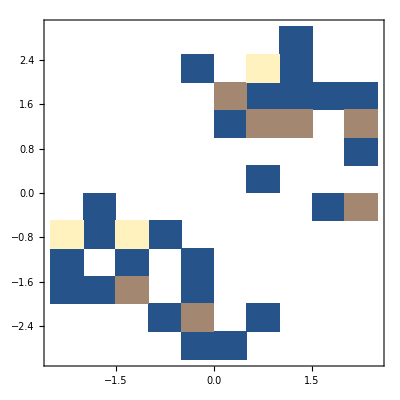

```mathematica
DensityHistogram[data,10]
```

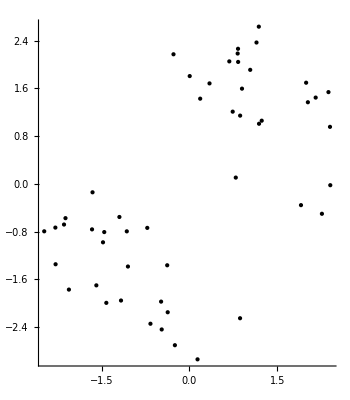

```mathematica
Graphics[Point[data],Axes->True]
```

```mathematica
Export["data8_500.wdx",data]
```

data8_500.wdx

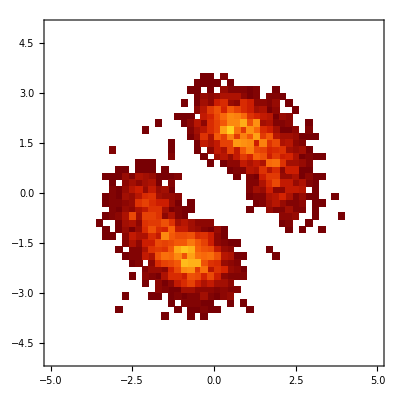
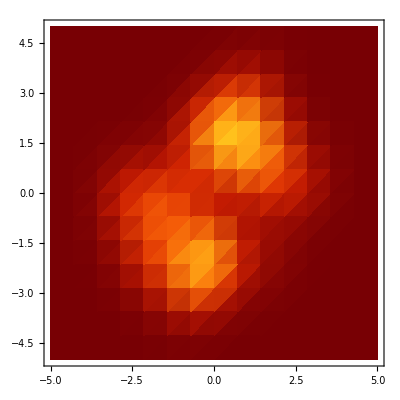
{-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
pointData=Import["data1_500.wdx","wdx"];
Do[
pointData=Join[pointData,Import[StringJoin["data",ToString[i],"_500.wdx"],"wdx"]];
,{i,2,8}]; (*4000*)
{DensityHistogram[pointData,25,ColorFunction->"SolarColors",PlotRange->{{-5,5},{-5,5}}] ,

SmoothDensityHistogram[data,ColorFunction->"SolarColors",PlotRange->{{-5,5},{-5,5}}],

Plot3D[fun[x,y],{x,-5,5},{y,-5,5},PlotRange->All,PlotPoints->100, ColorFunction->"SolarColors"]}
```